```mathematica
m={{2ep,0,-t,0,-t},{0,2ep,-t,-t,0},{-t,-t,2ed,0,0},{0,-t,0,0,0},{-t,0,0,0,0}}
```

{{2 ep,0,-t,0,-t},{0,2 ep,-t,-t,0},{-t,-t,2 ed,0,0},{0,-t,0,0,0},{-t,0,0,0,0}}

```mathematica
MatrixForm[m]
```

(2 ep | 0 | -t | 0 | -t
0 | 2 ep | -t | -t | 0
-t | -t | 2 ed | 0 | 0
0 | -t | 0 | 0 | 0
-t | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[m]
```

{ep-√(ep^2+t^2),ep+√(ep^2+t^2),Root[2 ed t^2+(4 ed ep-3 t^2) #1+(-2 ed-2 ep) #1^2+#1^3&,1],Root[2 ed t^2+(4 ed ep-3 t^2) #1+(-2 ed-2 ep) #1^2+#1^3&,2],Root[2 ed t^2+(4 ed ep-3 t^2) #1+(-2 ed-2 ep) #1^2+#1^3&,3]}

```mathematica
m2={{2ep,0,-t},{0,2ep,-t},{-t,-t,2ed}}
```

{{2 ep,0,-t},{0,2 ep,-t},{-t,-t,2 ed}}

```mathematica
MatrixForm[m2]
```

(2 ep | 0 | -t
0 | 2 ep | -t
-t | -t | 2 ed)

```mathematica
Eigenvalues[m2]
```

{2 ep,ed+ep-√(ed^2-2 ed ep+ep^2+2 t^2),ed+ep+√(ed^2-2 ed ep+ep^2+2 t^2)}

```mathematica
FullSimplify[%]
```

{2 ep,ed+ep-√((ed-ep)^2+2 t^2),ed+ep+√((ed-ep)^2+2 t^2)}

```mathematica
m3={{ed,-t Cos[ky],-t Cos[kx]},{-t Cos[ky],ep,0},{-t Cos[kx],0,ep}}
```

{{ed,-t Cos[ky],-t Cos[kx]},{-t Cos[ky],ep,0},{-t Cos[kx],0,ep}}

```mathematica
MatrixForm[m3]
```

(ed | -t Cos[ky] | -t Cos[kx]
-t Cos[ky] | ep | 0
-t Cos[kx] | 0 | ep)

```mathematica
m3//Eigenvalues//FullSimplify
```

{ep,1/2 (ed+ep-√((ed-ep)^2+4 t^2+2 t^2 (Cos[2 kx]+Cos[2 ky]))),1/2 (ed+ep+√((ed-ep)^2+4 t^2+2 t^2 (Cos[2 kx]+Cos[2 ky])))}

```mathematica
ev=Eigenvalues[m3]
```

{2 ep,1/2 (2 ed+2 ep-√2 √(2 ed^2-4 ed ep+2 ep^2+2 t^2+t^2 Cos[2 kx]+t^2 Cos[2 ky])),1/2 (2 ed+2 ep+√2 √(2 ed^2-4 ed ep+2 ep^2+2 t^2+t^2 Cos[2 kx]+t^2 Cos[2 ky]))}

```mathematica
Plot3D[ev/.ed->1/.ep->2/.t->1,{kx,-Pi,Pi},{ky,-Pi,Pi}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[ev/.ed->ed2/.ep->ep2/.t->t2,{kx,-Pi,Pi},{ky,-Pi,Pi},ColorFunction->"Rainbow"],{ed2,-1,1},{ep2,-1,1},{t2,-1,1}]
```

```mathematica
Solve[ee==(e+e0)/2-Sqrt[(e-e0)^2/4+δ],e,Reals]
```

{{e→ConditionalExpression[(e0 ee-ee^2+δ)/(e0-ee),(e0>ee&&δ>-e0^2+2 e0 ee-ee^2)||(e0<ee&&δ<-e0^2+2 e0 ee-ee^2)]}}

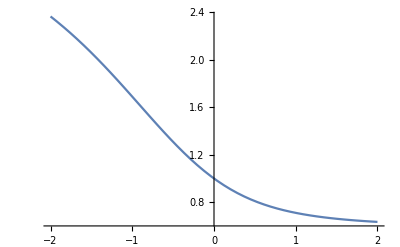

```mathematica
Plot[Sqrt[x^2/2+1]/(Sqrt[x^2/2+1]+x/2),{x,-2,2}]
```

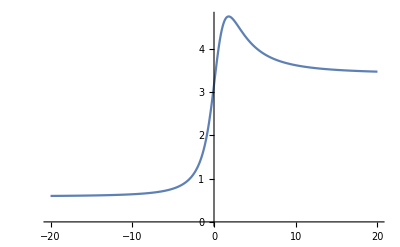

```mathematica
Plot[Sqrt[x^2/2+10]/(Sqrt[x^2/2+1]-x/2),{x,-20,20}]
```